```mathematica
(* color used for the contour plots*)
cd = ColorData[#]&/@{{"AvocadoColors","Reverse"},{"CoffeeTones","Reverse"},{"GrayTones","Reverse"}};

(* color used for the coexistence plot*)
valp = 0.45;
colx = CMYKColor[0,0,0,valp];
colxy = CMYKColor[0,valp,0,valp];
colxyz = CMYKColor[valp,valp,0,valp];
coly = CMYKColor[0,valp,0,0];
colyz = CMYKColor[valp,valp,0,0];
colz =  CMYKColor[valp,0,0,0.];
colxz=  CMYKColor[valp,0,0,valp];

(* darker color used for the time series*)
dval = 0.2;
colxx = CMYKColor[0,0,0,valp +dval ];
colyy = CMYKColor[0,valp +dval,0,0];
colzz =  CMYKColor[valp +dval,0,0,0.];

(* line type used for the time series*)
at = 2.5;
col ={{AbsoluteThickness[at],colxx},{AbsoluteThickness[at],colyy},{AbsoluteThickness[at],colzz}};
col2 ={{Dashed, AbsoluteThickness[at],colxx},{Dashed,AbsoluteThickness[at],colyy},{Dashed, AbsoluteThickness[at],colzz}};
col3 = {{Dotted, AbsoluteThickness[at],colxx},{Dotted,AbsoluteThickness[at],colyy},{Dotted, AbsoluteThickness[at],colzz}};

(* legend and axes label *)
lg= LineLegend[{col}, {{"Forest", "FMG", "GMG"}},LabelStyle->Directive[18,FontFamily->"Arial"]];
lb= Style[#, FontFamily->"Arial",18]&/@{"Time BP (yr) ", "Proprotion"};
is = 300;
ls = Directive[14, Black, FontFamily->"Arial"];

(* builds the color scheme for the coexistence by mapping a color to each communitu composition *)
CoexCol[temp_]:= Which[
temp[[1]] ≥ 0.005  && temp[[2]] ≥ 0.005  && temp[[3]] ≥ 0.005 , colxyz,
temp[[1]] ≥ 0.005 && temp[[2]] ≥ 0.005 && temp[[3]] < 0.005,colxy,
temp[[1]] ≥ 0.005 && temp[[2]] < 0.005 && temp[[3]] ≥ 0.005, colxz ,
temp[[1]] < 0.005 && temp[[2]] ≥ 0.005 && temp[[3]] ≥ 0.005,colyz ,
temp[[1]] ≥ 0.005 && temp[[2]] < 0.005 && temp[[3]] < 0.005,colx,
temp[[1]] < 0.005 && temp[[2]] ≥ 0.005 && temp[[3]] < 0.005, coly,
temp[[1]] < 0.005 && temp[[2]] < 0.005 && temp[[3]] ≥ 0.005, colz
];

(* default value for the colonization and mortalitu rate, the f and g are temporary*)
PARAM = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.943,g -> 0.9974}//Association;

(* the right hand side of the differential equations where all parameters are constant *)
MAT= {
 x[t] (cx (1 - x[t] -  f y[t] - g z[t])- mx) ,
y[t] (cy (1 - x[t]- y[t] -  g z[t])- my   - (1- f) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - mz - (1-g)(cx x[t] + cy y[t]))
};

(* the right hand side of the differential equations where F and G and MX are time dependent *)
FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

(* the right hand side of the differential equations where all parameters are time dependent, eventually not used *)
FMATC = {
 x[t] (CX[t] (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (CY[t] (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) CX[t] x[t]) , 
z[t] (CZ[t] (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(CX[t]x[t] + CY[t] y[t]))
};
```

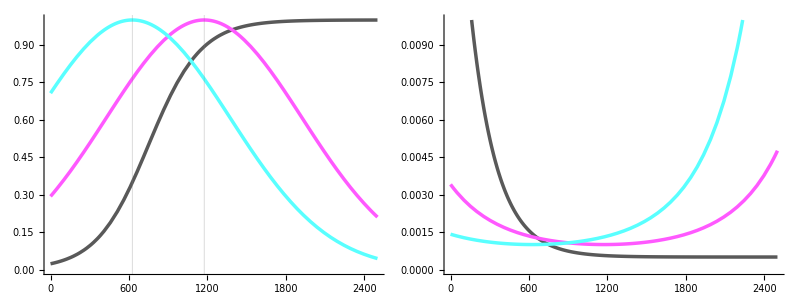

```mathematica
(* contructing the change in mortality as a function of precipitation, xx ,yy, and zz are the optimal precipitation for forest, fire-grass, and grazing-lawn *)
xx = 1725;

zz = 625;
vzz =750;
maxz = PDF[NormalDistribution[zz, vzz],zz];

yy = 1175;
vyy =750;
maxy = PDF[NormalDistribution[yy, vyy],yy];

Sx[t_]:=1/(1+  Exp[-0.005(t -750)]);
Sy[t_]:= PDF[NormalDistribution[yy,vyy],t]/maxy;
Sz[t_]:= PDF[NormalDistribution[zz,vzz],t]/maxz;

figNiche = Grid[{{Plot[{Sx[x], Sy[x], Sz[x]},{x,0,2500},PlotRange->{All,{0.,1}},GridLines->{{625, 1175}, None}, PlotStyle->col, ImageSize->300],Plot[{mx /Sx[t], my / Sy[t],mz/ Sz[t]} /.PARAM//Evaluate,{t, 0,2500},PlotRange-> {All,{0.,0.01}}, PlotStyle->col,ImageSize->300]}}]
```

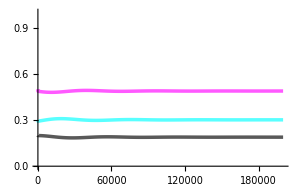
-Graphics-Time BP (yr) Proprotion

```mathematica
(* vestigial code, in case one wants to play with value of f and g *)
PP = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.943,g -> 0.9974}//Association;

(* constructing and solving the differential equations and plotting the solution*)
eqn = {
x'[t] ==MAT[[1]],
y'[t] ==MAT[[2]],
z'[t] == MAT[[3]] , 
x[0]==0.2,y[0]==0.5,z[0]==0.3}/.PP;

time = 200000;
sol= NDSolve[eqn,{x,y,z},{t,0,time},AccuracyGoal->20];
figX =
Labeled[
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)(*,0.5,0.3,0.2*)}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->ls,ImageSize->is],
lb,{Bottom,Left}, RotateLabel->True]
```

## Figure 1

### Map Madagascar: not used

```mathematica
GeoGraphics[{GeoStyling["Satellite"],Polygon[LinguisticAssistant]},GeoBackground->None];
```

```mathematica
fig1a = GeoGraphics[{GeoStyling["ContourMap",Contours->40],Polygon[LinguisticAssistant]},GeoBackground->None]
```

-Graphics-

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1a.png", fig1a, ImageResolution->200 ]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1a.png

### Temperature reconstruction

```mathematica
lb1 = Style[#, FontFamily->"Arial",18]&/@{"Time BP (yr)", "Precipitation (mm yr^-1)"};
```

```mathematica
(* vC is the scaling of the precipitation, var in the ms 
data from : Li,H.,Sinha,A.,André,A.A.,Spötl,C.,Vonhof,H.B.,Meunier,A.,...& Biswas,J.2020. A multimillennial climatic context for the megafaunal extinctions in Madagascar and Mascarene Islands.Science Advances,6(42):eabb2459
*)
vC = 300;
temp = Import["/Users/tanjona/Box Sync/projects/Grassland_Holocene/data/Li2020_speleo_Rodrigues.csv"][[3;;]];
temp1 = Interpolation[temp];
(* reverse time because solving the differential equation needs to go from t =0 to 8k*)
hum[t_] :=  yy -vC temp1[8000-t];
```

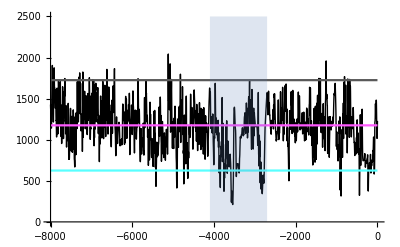
-Graphics-Time BP (yr)Precipitation (mm yr^-1)

```mathematica
(* plotting the time series*)
fig1b =Labeled[
Show[
Plot[{hum[8000-x],xx, yy,zz},{x,0,8000}, ScalingFunctions-> {"Reverse", Automatic}, AxesOrigin->{8000,0}, PlotStyle->{{AbsoluteThickness[1],Black},colxx,colyy,colzz}, LabelStyle->ls, PlotRange->{All, {0,2500}}],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
]
,lb1,{Bottom, Left}, RotateLabel->True]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1c.png", fig1b, ImageResolution->150 ]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1c.png

#### Recycle

```mathematica
l1b = Style[#, FontFamily->"Arial",14]&/@{"Time BP (year)", "ΔTemperature (°C)"};
```

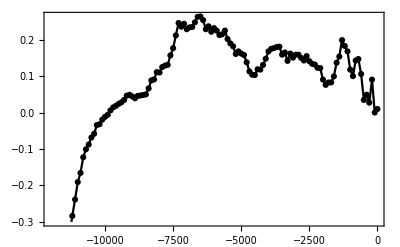
-Graphics-Time BP (year)ΔTemperature (°C)

```mathematica
(* temperature reconstruction, data from: Kaufman,D.,McKay,N.,Routson,C.,Erb,M.,Dätwyler,C.,Sommer,P.S.,Oliver,O.& Davis,B.2020. Holocene global mean surface temperature,a multi-method reconstruction approach. Scientific Data,7(1),1-13.*)
temp = Import["/Users/tanjona/Box Sync/projects/Grassland_Holocene/data/Temperature_data.csv"][[2;;,{2,1}]];
fig1b =
Labeled[
 ListPlot[temp, ScalingFunctions->{"Reverse", Automatic},AxesOrigin->{11500, 0},Joined->True, PlotMarkers->Automatic,PlotStyle->Black, LabelStyle->Directive[14, FontFamily->"Arial",Black], Frame->True]
,l1b, {Bottom,Left},RotateLabel->True]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1b.png", fig1b, ImageResolution->200 ]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1b.png

```mathematica
(* temperature and precipitation from worldclim, an attempt to see if it can be used in the model *)
clim = Import["/Users/tanjona/Box Sync/projects/Grassland_Holocene/data/temperature.csv"];
```

```mathematica
Dimensions@clim
```

{799020,5}

```mathematica
clim2 = Select[clim, #[[2]] ==  1 ||#[[2]] == 2  ||#[[2]] == 14 &][[All,{2,-2,-1}]];
```

```mathematica
Mean[clim2]
```

{898564/614929,20.3813,1339.17}

```mathematica
(* No consistent trends/correlation *)
ListPlot[clim2[[All,{2,3}]]]
```

-Graphics-

```mathematica
l1b = Style[#, FontFamily->"Arial",14]&/@{"Time BP (year)", "ΔTemperature (°C)"};
```

```mathematica
[[2;;,{2,1}]]
```

### Environmental niche

```mathematica
lb1c = Style[#, FontFamily->"Arial",18]&/@{ "Precipitation (mm yr^-1)", "Mortality rate"};
```

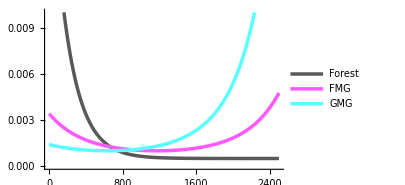
-Graphics-Precipitation (mm yr^-1)Mortality rate

```mathematica
fig1c=Legended[Labeled[Plot[{mx /Sx[t], my / Sy[t],mz/ Sz[t]} /.PARAM//Evaluate,{t, 0,2500},PlotRange-> {All,{0.,0.01}}, PlotStyle->col,ImageSize->300, LabelStyle->ls],lb1c, {Bottom,Left}, RotateLabel->True],lg]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1b.png", fig1c, ImageResolution->150 ]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig1b.png

## Figure 2

### Default tree mortality (only commenting this section) all the codes below is a copy paste with minor change

```mathematica
(* Exploring the change in f and g *)
res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];
,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res1 = res;
```

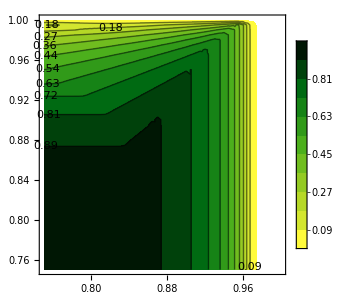
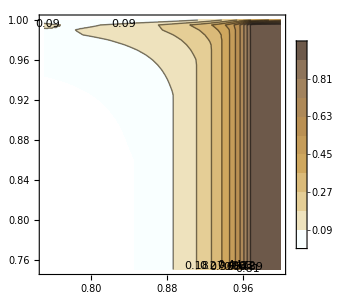
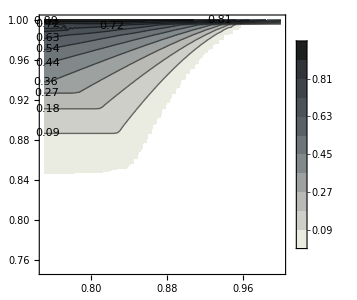
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* change in relative density, forest, fire-grass, and grazing-lawn *)fig21 =Grid[{Table[ListContourPlot[Association[res1][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
(* Building the color pattern for the coexistence plot based on the relative density above *) 
res1a = Association@res1;
Do[
temp = Flatten[Values@res1[[i]],1];
ky = Flatten[Keys[res1[[i]]],1];
res1a[ky] = CoexCol[temp];
,{i, Length[res1]}]
```

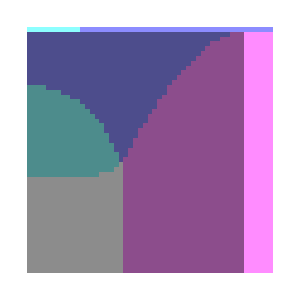

```mathematica
(* A bit trick to map the colors, so using ArrayPlot instead of Contour or Density (Mathematica cannot stop interpolating the data). The x and y axis have to be manually created *)
res1b= Reverse[Transpose@Partition[Values@res1a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig21b =ArrayPlot[res1b, FrameTicks->ft,LabelStyle->ls,  ImageSize->is]
```

### Double tree mortality

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->2 0.0005, my -> 0.001, mz -> 0.001, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res2= res;
```

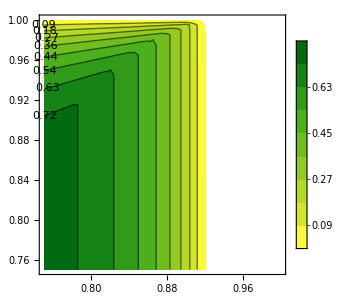
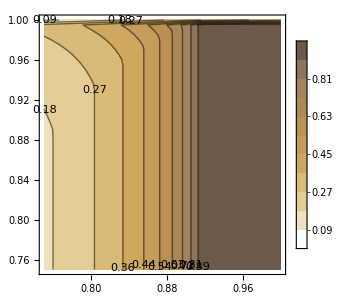
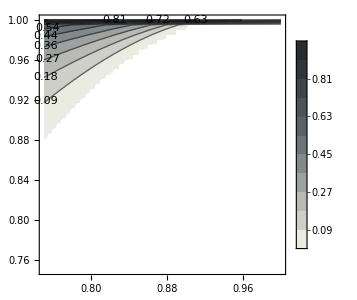
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig22 =Grid[{Table[ListContourPlot[Association[res2][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res2a = Association@res2;
Do[
temp = Flatten@Values@res2[[i]];
ky = Flatten@Keys[res2[[i]]];
res2a[ky] = CoexCol[temp];
,{i, Length[res2]}]
```

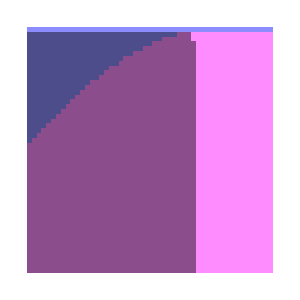

```mathematica
res2b = Reverse[Transpose@Partition[Values@res2a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig22b =ArrayPlot[res2b, FrameTicks->ft, LabelStyle->ls, ImageSize->is]
```

### With climate niche, mortality, using optim x = 1725

```mathematica
tMX =  mx/ Sx[xx]/.PARAM  ; 
tMY = my/ Sy[xx]/.PARAM  ;
tMZ = mz /Sz[xx]/.PARAM  ;
```

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res3= res;
```

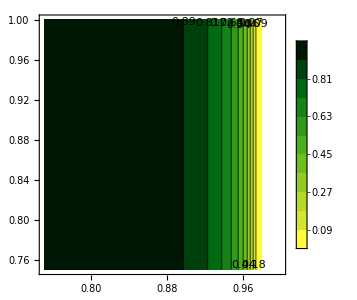
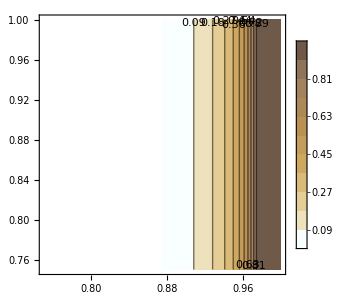
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig23 =Grid[{Table[ListContourPlot[Association[res3][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res3a = Association@res3;
Do[
temp = Flatten@Values@res3[[i]];
ky = Flatten@Keys[res3[[i]]];
res3a[ky] = CoexCol[temp];
,{i, Length[res3]}]
```

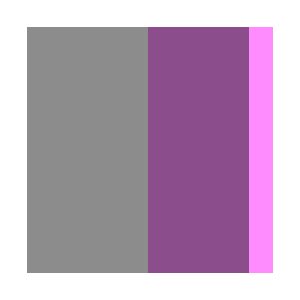

```mathematica
res3b = Reverse[Transpose@Partition[Values@res3a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig23b =ArrayPlot[res3b, FrameTicks->ft, LabelStyle->ls, ImageSize->is]
```

### With climate niche, mortality using optim y = 1175

```mathematica
tMX =  mx/ Sx[yy]/.PARAM  ; 
tMY = my/ Sy[yy]/.PARAM  ;
tMZ = mz /Sz[yy]/.PARAM  ;
```

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res4= res;
```

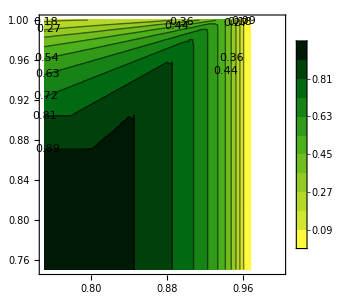
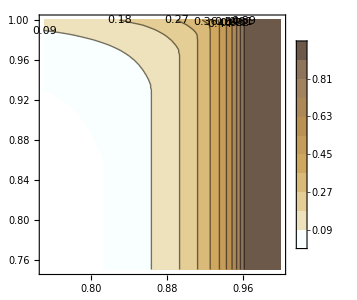
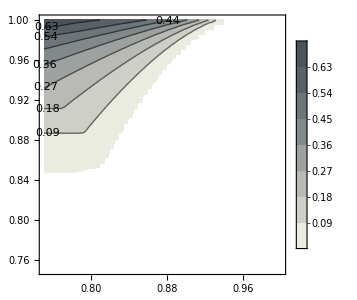
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig34 =Grid[{Table[ListContourPlot[Association[res4][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res4a = Association@res4;
Do[
temp = Flatten@Values@res4[[i]];
ky = Flatten@Keys[res4[[i]]];
res4a[ky] = CoexCol[temp];
,{i, Length[res4]}]
```

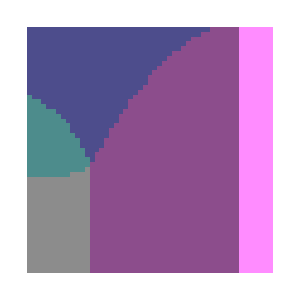

```mathematica
res4b = Reverse[Transpose@Partition[Values@res4a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig24b =ArrayPlot[res4b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### With climate niche, mortality using optim z = 625

```mathematica
tMX =  mx/ Sx[zz]/.PARAM  ; 
tMY = my/ Sy[zz]/.PARAM  ;
tMZ = mz /Sz[zz]/.PARAM  ;

res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res5= res;
```

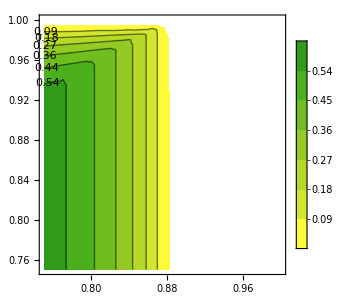
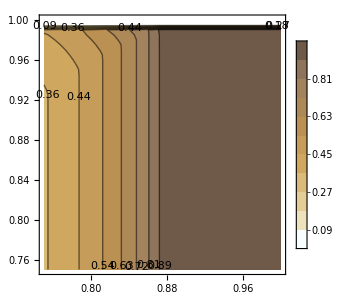
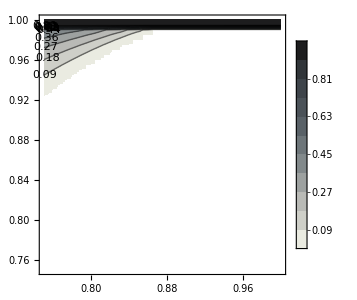
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig35 =Grid[{Table[ListContourPlot[Association[res5][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res5a = Association@res5;
Do[
temp = Flatten@Values@res5[[i]];
ky = Flatten@Keys[res5[[i]]];
res5a[ky] = CoexCol[temp];
,{i, Length[res5]}]
```

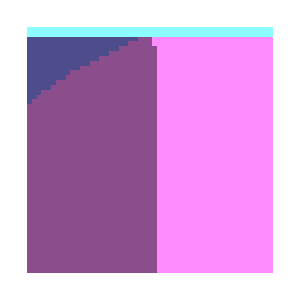

```mathematica
res5b = Reverse[Transpose@Partition[Values@res5a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig25b=ArrayPlot[res5b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### With climate niche, colonization using optim x = 1725

```mathematica
tCX =  cx Sx[xx]/.PARAM  ; 
tCY = cy Sy[xx]/.PARAM  ;
tCZ = cz Sz[xx]/.PARAM  ;

res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> tCX, cy -> tCY, cz -> tCZ, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res6= res;
```

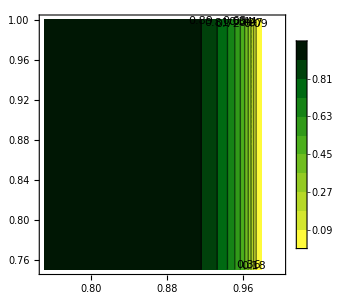
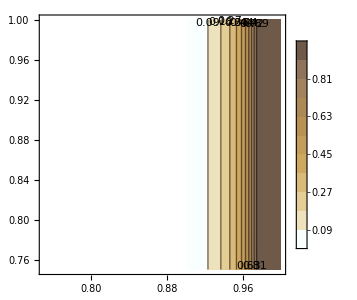
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig26 =Grid[{Table[ListContourPlot[Association[res6][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res6a = Association@res6;
Do[
temp = Flatten@Values@res6[[i]];
ky = Flatten@Keys[res6[[i]]];
res6a[ky] = CoexCol[temp]
,{i, Length[res6]}]
```

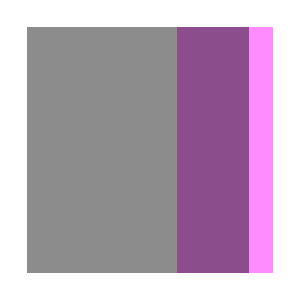

```mathematica
res6b = Reverse[Transpose@Partition[Values@res6a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig26b =ArrayPlot[res6b, FrameTicks->ft, LabelStyle->ls, ImageSize->is]
```

### With climate niche, colonization using optim y= 1175

```mathematica
tCX =  cx Sx[yy]/.PARAM  ; 
tCY = cy Sy[yy]/.PARAM  ;
tCZ = cz Sz[yy]/.PARAM  ;

res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> tCX, cy -> tCY, cz -> tCZ, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res7= res;
```

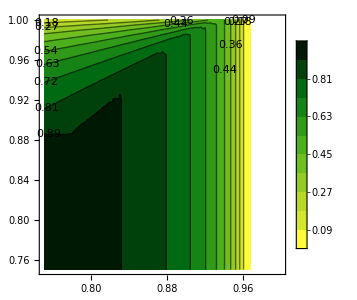
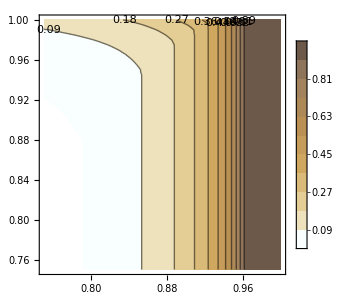
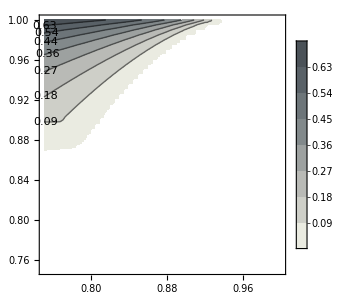
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig27 =Grid[{Table[ListContourPlot[Association[res7][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res7a = Association@res7;
Do[
temp = Flatten@Values@res7[[i]];
ky = Flatten@Keys[res7[[i]]];
res7a[ky] = CoexCol[temp];
,{i, Length[res7]}]
```

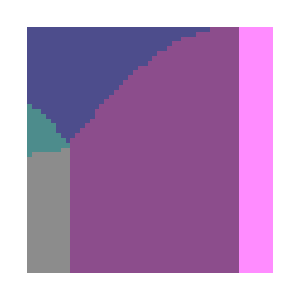

```mathematica
res7b = Reverse[Transpose@Partition[Values@res7a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig27b =ArrayPlot[res7b, FrameTicks->ft, LabelStyle->ls, ImageSize->is]
```

### With climate niche, colonization using optim z = 625

```mathematica
tCX =  cx Sx[zz]/.PARAM  ; 
tCY = cy Sy[zz]/.PARAM  ;
tCZ = cz Sz[zz]/.PARAM  ;

res = {};
INIT = {0.3,0.3,0.3};
Do[
param= {cx -> tCX, cy -> tCY, cz -> tCZ, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> ff,g -> gg}//Association;
(*Print[ff, "_",gg];*)
mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{ff,gg}->Chop@ out |>];

,{ff, 0.75,1.,0.005},{gg, 0.75,1,0.005}];
res8= res;
```

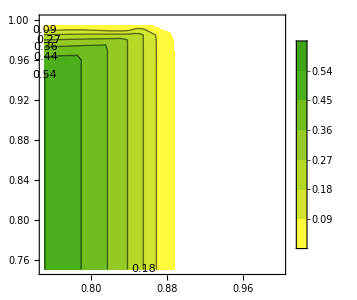
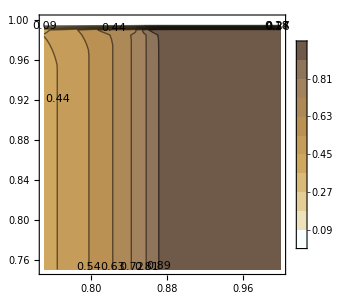
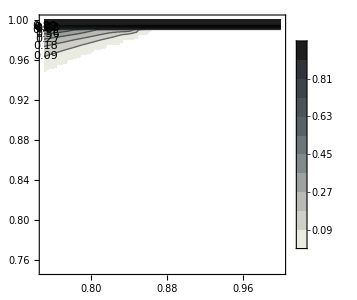
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig28 =Grid[{Table[ListContourPlot[Association[res8][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.005,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res8a = Association@res8;
Do[
temp = Flatten@Values@res8[[i]];
ky = Flatten@Keys[res8[[i]]];
res8a[ky] = CoexCol[temp];
,{i, Length[res8]}]
```

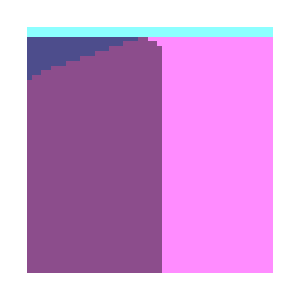

```mathematica
res8b = Reverse[Transpose@Partition[Values@res8a,51]];
ft = {Transpose[{Range[1,51,10],Range[1, 0.75,-0.05]}],Transpose@{Range[1,51,10],Range[ 0.75,1,0.05]}};
fig28b =ArrayPlot[res8b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### Compile pannels

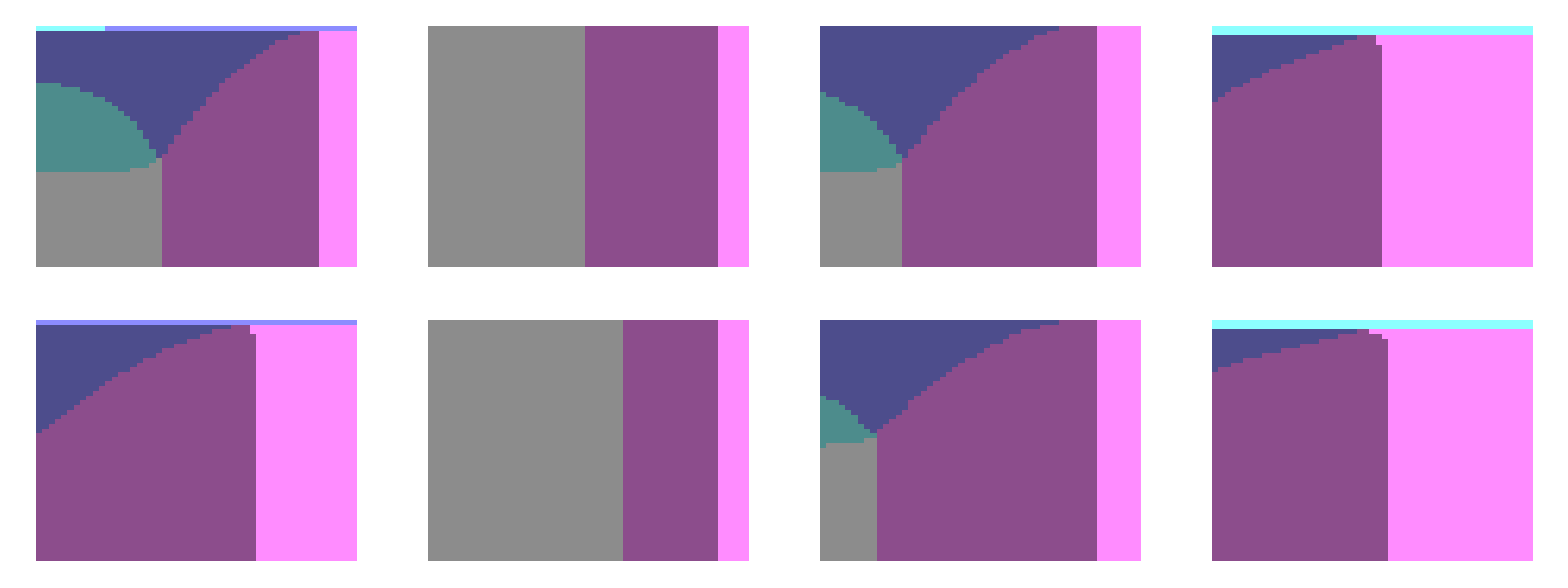

```mathematica
fig2a = Grid[Transpose@{{fig21b, fig22b},{fig23b, fig26b},{fig24b, fig27b},{fig25b, fig28b}},Spacings->{1.5,5}]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2_coex.png",fig2a, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2_coex.png

```mathematica
lbb = Style[#, 20, Black, FontFamily->"Arial"]&/@ {"Fire regime (f)", "Grazing efficiency (g)"};
ptitle = Style[#, 20, Black, FontFamily->"Arial"]&/@ {"High", "Intermediate", "Low"};
fig2 = Labeled[Grid[{{Style["Precipitation", 20, Black, FontFamily->"Arial"], SpanFromLeft},ptitle,{fig23b, fig24b,fig25b}}, Spacings->{Automatic,{1,1}}],lbb, {Bottom,Left},RotateLabel->True]
```

Precipitation |  | 
High | Intermediate | Low
-Graphics- | -Graphics- | -Graphics-Fire regime (f)Grazing efficiency (g)

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2.png",fig2, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2.png

```mathematica
cout = Rotate[#, 180 Degree]&/@(StringJoin@@@Subsets[{"X","Y","Z"},{1,3}])
```

{X,Y,Z,XY,XZ,YZ,XYZ}

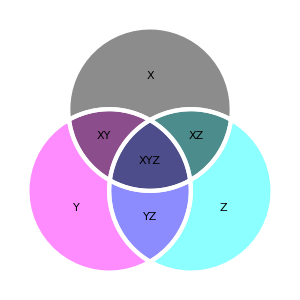

```mathematica
a=Disk[{0,1}];
b=Disk[{-0.5,0}];
c=Disk[{0.5,0}];
subsets=Subsets[{a,b,c},{1,3}];

subsetscolors= {colx,coly,colz,colxy,colxz,colyz,colxyz};

legFig2 = RegionPlot[Evaluate[DiscretizeRegion[RegionDifference[BooleanRegion[And,#],BooleanRegion[Or,Complement[{a,b,c,EmptyRegion[2]},#]]]]&/@subsets],PlotLabels->Callout[cout,Center],Sequence[PlotStyle->subsetscolors,BoundaryStyle->Directive[Thickness[0.01],White],Frame->False,LabelStyle->{24},PerformanceGoal->"Speed",ImageSize->300]]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2_coex_leg.png",legFig2, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig2_coex_leg.png

## Figure 3: vary niche and deforestation

```mathematica
t0  = 200;
dp = 400;
dt = 1000;
```

### f = 0.825, g = 0.975, same code as above but fixed f and g and vary mortality and and precipitation

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
tMX =  pmx mx +  mx/ Sx[yy + cc] /.PARAM;
tMY = my/Sy[yy+ cc]/.PARAM;
tMZ= mz/Sz[yy + cc]/.PARAM;

param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> 0.825,g -> 0.975}//Association;

mat = MAT/.param;

time = 200000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{pmx,cc + yy}->Chop@ out |>];

,{pmx, 0,2.,0.05},{cc, -400,400,20}];
res9= res;
```

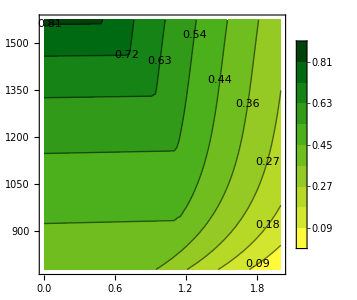
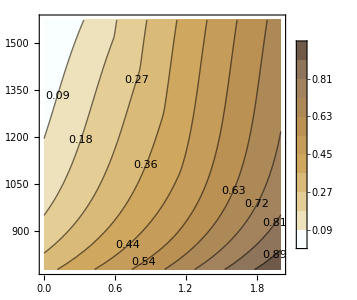
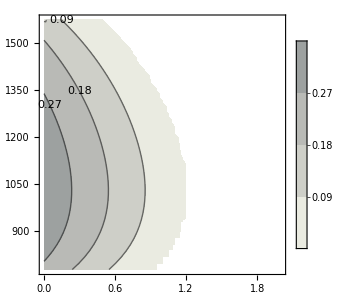
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig41 =Grid[{Table[ListContourPlot[Association[res9][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
lb2 = Style[#, 20, Black, FontFamily->"Arial"]&/@ {"Relative increse in mortaility rate due to deforestation", "Precipitation (mm yr^-1)"};
```

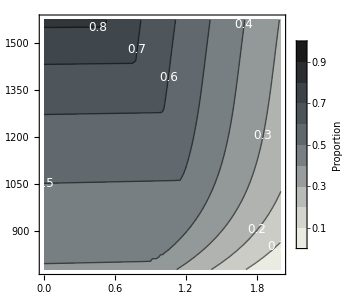
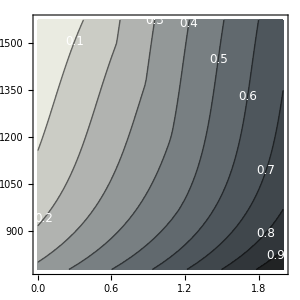
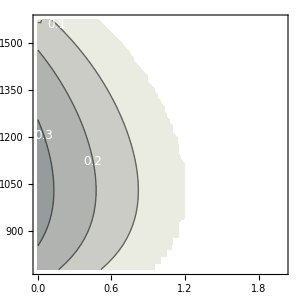
Forest | FMG | GMG
-Graphics- | -Graphics- | -Graphics-Relative increse in mortaility rate due to deforestationPrecipitation (mm yr^-1)

```mathematica
fig41a =Labeled[
Legended[Grid[{Style[#, 20, FontFamily->"Arial"]&/@{"Forest", "FMG", "GMG"},Table[ListContourPlot[Association[res9][[All,i]],InterpolationOrder->1,Contours->Range[0.1,1,0.1],ContourLabels->(Text[Style[#3,White,12],{#1,#2}]&)
, ColorFunctionScaling->False,ColorFunction->ColorData[{"GrayTones", "Reverse"}],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}],BarLegend[{{"GrayTones","Reverse"},{0,1}},9,LabelStyle-> 14,LegendLabel->Style["Proportion", 18, FontFamily->"Arial"]]],
lb2,{Bottom, Left}, RotateLabel->True]
```

```mathematica
res9a = Association@res9;
Do[
temp = Flatten@Values@res9[[i]];
ky = Flatten@Keys[res9[[i]]];
res9a[ky] = CoexCol[temp];
,{i, Length[res9]}]
```

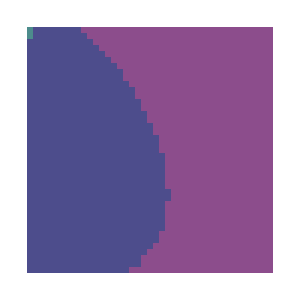

```mathematica
res9b = Reverse[Transpose@Partition[Values@res9a,41]];
ft = {Transpose[{Range[1,41,10],Range[yy + 400,yy -400, -200]}],Transpose@{Range[1,41,10],Range[ 1.,3,0.5]}};
fig41a =ArrayPlot[res9b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### f = 0.825, g = 0.995

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
tMX =  pmx mx + mx/ Sx[yy + cc] /.PARAM;
tMY = my/Sy[yy+ cc]/.PARAM;
tMZ= mz/Sz[yy + cc]/.PARAM;

param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> 0.825,g -> 0.995}//Association;

mat = MAT/.param;

time = 200000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{pmx,cc}->Chop@ out |>];

,{pmx, 0,2.,0.05},{cc, -400,400,20}];
res10= res;
```

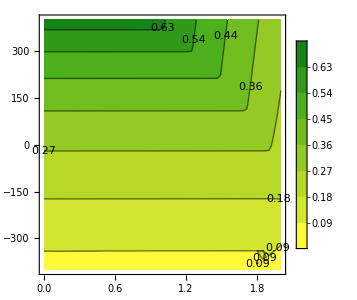
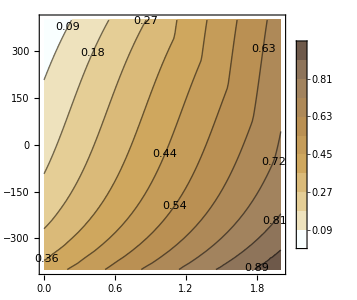
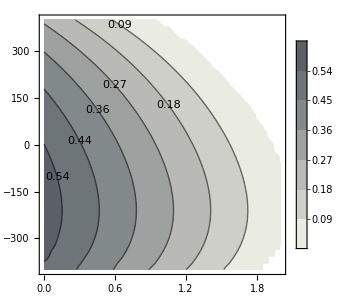
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig42 =Grid[{Table[ListContourPlot[Association[res10][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

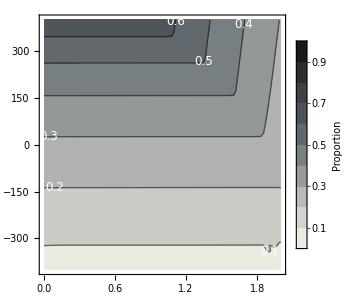
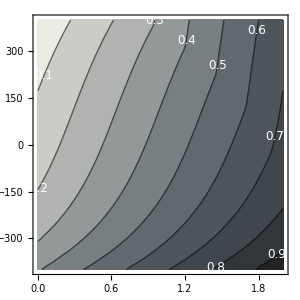
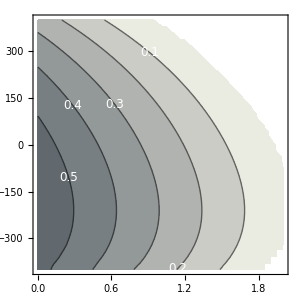
Forest | Fire-grass | Grazing-lawn
-Graphics- | -Graphics- | -Graphics-Relative increse in mortaility rate due to deforestationPrecipitation (mm yr^-1)

```mathematica
fig42a =Labeled[
Legended[Grid[{Style[#, 20, FontFamily->"Arial"]&/@{"Forest", "FMG", "GMG"},Table[ListContourPlot[Association[res10][[All,i]],InterpolationOrder->1,Contours->Range[0.1,1,0.1],ContourLabels->(Text[Style[#3,White,12],{#1,#2}]&)
, ColorFunctionScaling->False,ColorFunction->ColorData[{"GrayTones", "Reverse"}],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}],BarLegend[{{"GrayTones","Reverse"},{0,1}},9,LabelStyle-> 14,LegendLabel->Style["Proportion", 18, FontFamily->"Arial"]]],
lb2,{Bottom, Left}, RotateLabel->True]
```

```mathematica
res10a = Association@res10;
Do[
temp = Flatten@Values@res10[[i]];
ky = Flatten@Keys[res10[[i]]];
res10a[ky] = CoexCol[temp];
,{i, Length[res10]}]
```

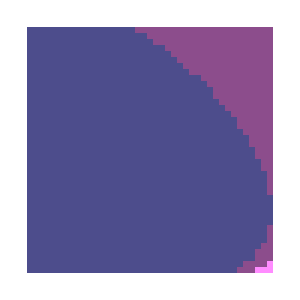

```mathematica
res10b = Reverse[Transpose@Partition[Values@res10a,41]];
ft = {Transpose[{Range[1,41,10],Range[yy + 400,yy -400, -200]}],Transpose@{Range[1,41,10],Range[ 1.,3,0.5]}};
fig42a =ArrayPlot[res10b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### f = 0.725, g = 0.975

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
tMX =  pmx mx +  mx/ Sx[yy + cc] /.PARAM;
tMY = my/Sy[yy+ cc]/.PARAM;
tMZ= mz/Sz[yy + cc]/.PARAM;

param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> 0.725,g -> 0.975}//Association;

mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{pmx,cc}->Chop@ out |>];

,{pmx, 0,2.,0.05},{cc, -400,400,20}];
res11= res;
```

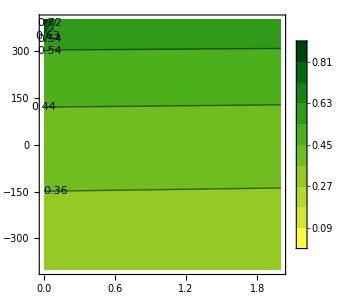
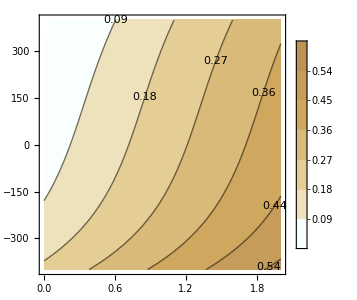
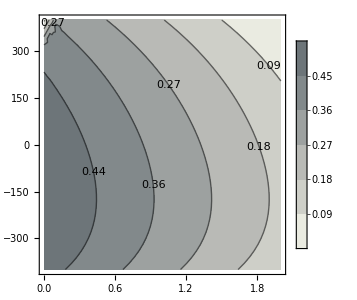
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig43 =Grid[{Table[ListContourPlot[Association[res11][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res11a = Association@res11;
Do[
temp = Flatten@Values@res11[[i]];
ky = Flatten@Keys[res11[[i]]];
res11a[ky] = CoexCol[temp];
,{i, Length[res11]}]
```

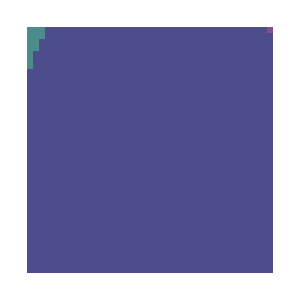

```mathematica
res11b = Reverse[Transpose@Partition[Values@res11a,41]];
ft = {Transpose[{Range[1,41,10],Range[yy + 400,yy -400, -200]}],Transpose@{Range[1,41,10],Range[ 1.,3,0.5]}};
fig42a =ArrayPlot[res11b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### f = 0.925, g = 0.995

```mathematica
res = {};
INIT = {0.3,0.3,0.3};
Do[
tMX =  pmx mx + mx/ Sx[yy + cc] /.PARAM;
tMY = my/Sy[yy+ cc]/.PARAM;
tMZ= mz/Sz[yy + cc]/.PARAM;

param= {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->tMX, my -> tMY, mz -> tMZ, f -> 0.925,g -> 0.995}//Association;

mat = MAT/.param;

time = 100000;
sol= NDSolve[{x'[t] == mat[[1]], y'[t] == mat[[2]], z'[t] == mat[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]},{x,y,z},{t,0,time},AccuracyGoal->10];
out = Flatten[{x[time], y[time], z[time]}/. sol];
AppendTo[res, <|{pmx,cc}->Chop@ out |>];

,{pmx, 0,2.,0.05},{cc, -400,400,20}];
res12= res;
```

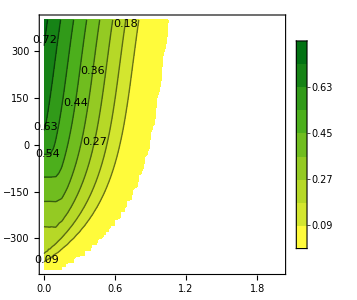
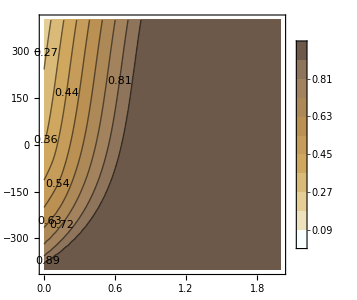
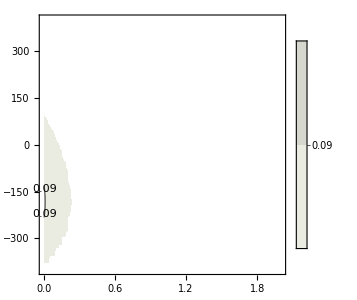
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig44 =Grid[{Table[ListContourPlot[Association[res12][[All,i]],InterpolationOrder->1,PlotLegends->Automatic,Contours->10,ContourLabels->10, ColorFunctionScaling->False, ColorFunction->cd[[i]],PlotRange->{All,All,{0.0001,1}}, ImageSize->is, LabelStyle->ls],{i, 3}]}]
```

```mathematica
res12a = Association@res12;
Do[
temp = Flatten@Values@res12[[i]];
ky = Flatten@Keys[res12[[i]]];
res12a[ky] = CoexCol[temp];
,{i, Length[res12]}]
```

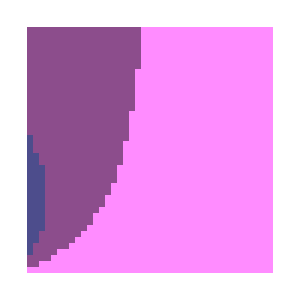

```mathematica
res12b = Reverse[Transpose@Partition[Values@res12a,41]];
ft = {Transpose[{Range[1,41,10],Range[yy + 400,yy -400, -200]}],Transpose@{Range[1,41,10],Range[ 1.,3,0.5]}};
fig43a =ArrayPlot[res12b, FrameTicks->ft,LabelStyle->ls, ImageSize->is]
```

### Compile

```mathematica
fig41a
```

Forest | FMG | GMG
-Graphics- | -Graphics- | -Graphics-Relative increse in mortaility rate due to deforestationPrecipitation (mm yr^-1)

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig3_defor_clim.png",fig41a, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig3_defor_clim.png

## Figure 4: transient and time-varying parameter

```mathematica
t0  = 200; (* time where the change occurs *)
 dt = 1000; (* duration of the change *)
```

### Patterns of deforestation without niche

```mathematica
PARAM3a = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;
pmx =0.8; (* additional mortality rate relative to mx *)
```

```mathematica
(* just used to find the initial conditions INIT *)
MX[t_] :=mx/.PARAM3a ; 
MY[t_] := my/.PARAM3a ;
MZ[t_] :=mz /.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten; 

(* find the equilibrium with deforestation, used for the dots in Fig 4*)
MX[t_] :=pmx mx + mx/.PARAM3a ; 
MY[t_] := my/.PARAM3a ;
MZ[t_] :=mz/.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINIT= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

(* find the intercept and regression for the linear trend *)
lin = Solve[{ mx == aa t0 + bb , pmx mx +  mx == aa (t0 +  dt) + bb},{aa,bb}]/.PARAM3a;

(* location of dots in Fig 4*)
XYF = Partition[Transpose[{ConstantArray[t0 +dt-30,3],FINIT}],1];
```

#### Abrupt trend

```mathematica
MX[t_] := If[t < t0,mx,pmx mx +  mx]/.PARAM3a ; 
MY[t_] := my/.PARAM3a ;
MZ[t_] :=mz /.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Linear trend

```mathematica
MX[t_] := Which[t < t0,mx, t0 ≤ t < t0 + dt, aa t + bb /. lin[[1]] , t0 + dt ≥ t,  pmx mx + mx]/.PARAM3a ; 
MY[t_] := my/.PARAM3a ;
MZ[t_] :=mz /.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol2= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Figure

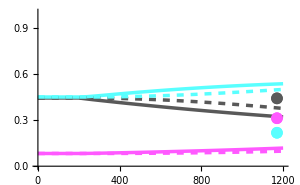
-Graphics-Time BP (yr) Proprotion

```mathematica
fig3a =
Labeled[
Show[
Plot[Evaluate[{x[t],y[t],z[t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t]}/.sol2], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]]],
lb,{Bottom,Left}, RotateLabel->True]
```

### Patterns of deforestation with niche

```mathematica
PARAM3a = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;
pmx =0.8;
```

```mathematica
MX[t_] :=mx/Sx[yy]/.PARAM3a ; 
MY[t_] := my/Sy[yy]/.PARAM3a ;
MZ[t_] :=mz/Sz[yy] /.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

MX[t_] :=pmx mx + mx/Sx[yy]/.PARAM3a ; 
MY[t_] := my/Sy[yy]/.PARAM3a ;
MZ[t_] :=mz/Sz[yy]/.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINIT= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

lin = Solve[{ mx/Sx[yy] == aa t0 + bb , pmx mx +  mx/Sx[yy] == aa (t0 +  dt) + bb},{aa,bb}]/.PARAM3a;

XYF = Partition[Transpose[{ConstantArray[t0 +dt-30,3],FINIT}],1];
```

#### Abrupt trend

```mathematica
(* Building the function to make mx abruptly change at t = 200  *)
MX[t_] := If[t < t0,mx/Sx[yy],pmx mx +  mx/Sx[yy]]/.PARAM3a ; 
MY[t_] := my/Sy[yy]/.PARAM3a ;
MZ[t_] :=mz /Sz[yy]/.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Linear trend

```mathematica
(* Building the function to make mx linearly change at t = 200  *)
MX[t_] := Which[t < t0,mx/Sx[yy], t0 ≤ t < t0 + dt, aa t + bb /. lin[[1]] , t0 + dt ≥ t,  pmx mx + mx/Sx[yy]]/.PARAM3a ; 
MY[t_] := my/.PARAM3a ;
MZ[t_] :=mz /.PARAM3a ;

F[t_]:= f /.PARAM3a  ;
G[t_] :=g /.PARAM3a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol2= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Figure

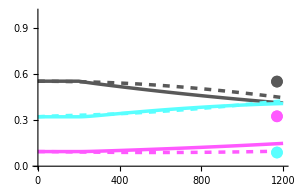
-Graphics-Time BP (yr) Proprotion

```mathematica
fig3b =
Labeled[
Show[
Plot[Evaluate[{x[t],y[t],z[t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t]}/.sol2], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]]],
lb,{Bottom,Left}, RotateLabel->True]
```

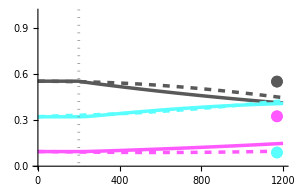

```mathematica
fig3bb =
Show[
Plot[Evaluate[{x[t],y[t],z[t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t]}/.sol2], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]],
GridLines-> { {200}, None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]]
```

### Patterns of climate change

```mathematica
PARAM3b = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;
nyy = yy - 525; (* this is the dryier climate *)
```

```mathematica
MX[t_] := mx/ Sx[yy]/.PARAM3b  ; 
MY[t_] := my/ Sy[yy]/.PARAM3b  ;
MZ[t_] :=mz /Sz[yy]/.PARAM3b  ;

F[t_]:= f /.PARAM3b  ;
G[t_] :=g /.PARAM3b ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3b,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;


MX[t_] := mx/ Sx[nyy]/.PARAM3b ; 
MY[t_] := my/ Sy[nyy]/.PARAM3b;
MZ[t_] :=mz /Sz[nyy]/.PARAM3b ;

F[t_]:= f /.PARAM3b  ;
G[t_] :=g /.PARAM3b ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3b,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINIT= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

linX = Solve[{ mx/Sx[yy] == aa t0 + bb , mx/Sx[nyy] == aa (t0 +  dt) + bb},{aa,bb}]/.PARAM3b;
linY = Solve[{ my/Sy[yy] == aa t0 + bb , my/Sy[nyy] == aa (t0 +  dt) + bb},{aa,bb}]/.PARAM3b;
linZ = Solve[{ mz/Sz[yy] == aa t0 + bb , mz/Sz[nyy] == aa (t0 +  dt) + bb},{aa,bb}]/.PARAM3b;

XYF = Partition[Transpose[{ConstantArray[t0 +dt-30,3],FINIT}],1];
```

#### Abrupt trend

```mathematica
(* Building the function to make all m abruptly change at t = 200 due to drying *)
MX[t_] := If[t < t0, mx/Sx[yy], mx/Sx[nyy]]/.PARAM3b ; 
MY[t_] := If[t < t0,my/Sy[yy], my/Sy[nyy]]/.PARAM3b ; 
MZ[t_] := If[t < t0,mz/Sz[yy], mz/ Sz[nyy]]/.PARAM3b ; 

F[t_]:= f /.PARAM3b  ;
G[t_] :=g /.PARAM3b ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3b,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Linear trend

```mathematica
(* Building the function to make all m linearly change at t = 200 due to drying *)
MX[t_] := Which[t < t0,mx/Sx[yy], t0 ≤ t < t0 + dt, aa t + bb /. linX[[1]] , t0 + dt ≥ t,   mx/Sx[nyy]]/.PARAM3b ; 
MY[t_] := Which[t < t0,my/Sy[yy], t0 ≤ t < t0 + dt, aa t + bb /. linY[[1]] , t0 + dt ≥ t,   my/Sy[nyy]]/.PARAM3b ; 
MZ[t_] := Which[t < t0,mz/Sz[yy], t0 ≤ t < t0 + dt, aa t + bb /. linZ[[1]] , t0 + dt ≥ t,   mz/Sz[nyy]]/.PARAM3b ; 

F[t_]:= f /.PARAM3b  ;
G[t_] :=g /.PARAM3b ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol2= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM3b,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Figure

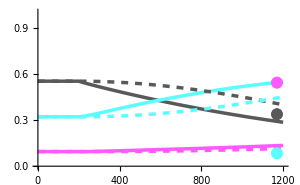
-Graphics-Time BP (yr) Proprotion

```mathematica
fig3c =
Labeled[
Show[
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol2], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]]],
lb,{Bottom,Left}, RotateLabel->True]
```

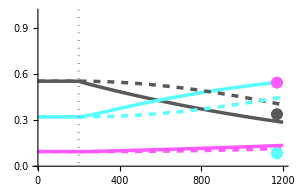

```mathematica
fig3cc =
Show[
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol2], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}],
ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12], AxesOrigin->{0,0}]
, GridLines->{{200}, None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]
]
```

### Compile panels

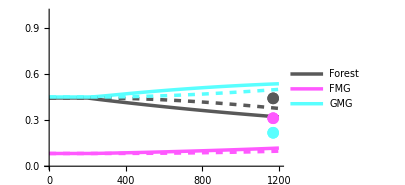
-Graphics-Time BP (yr) Proprotion | -Graphics-Time BP (yr) Proprotion | -Graphics-Time BP (yr) Proprotion

```mathematica
fig4old = Legended[Grid[{{fig3a,fig3b,fig3c}}, Spacings->0.5],lg]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig4_transient.png",fig4, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig4_transient.png

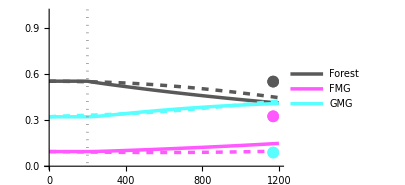
Deforestation | Drying
-Graphics- | -Graphics-Time BP (yr) Proprotion

```mathematica
fig4 = Legended[
Labeled[Grid[{Style[#, 18, FontFamily->"Arial"]&/@{"Deforestation","Drying"},{fig3bb,fig3cc}}, Spacings->0.5],
lb,{Bottom,Left}, RotateLabel->True]
,lg]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig4_transient.pdf",fig4, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig4_transient.pdf

## Recycle. Alternative Figure 4: Combined abrupt change

```mathematica
t0  = 200;
dp = 400; (* this creates a delay for the start of the other change *)
dt = 1000;
```

### Patterns of climate change

```mathematica
PARAM4a = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;
nyy = yy - 400;
pmx = 1.5;
```

```mathematica
(* EQUILIBRIUM TO USE AS INITIAL CONDITIONS*)
MX[t_] := mx/ Sx[yy]/.PARAM4a  ; 
MY[t_] := my/ Sy[yy]/.PARAM4a ;
MZ[t_] :=mz /Sz[yy]/.PARAM4a  ;

F[t_]:= f /.PARAM4a  ;
G[t_] :=g /.PARAM4a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

(* FINAL EQUILIBRIUM INCLUDING DEFORESTATION and CLIMATE CHANGE *)
MX[t_] := pmx mx/ Sx[nyy]/.PARAM4a ; 
MY[t_] := my/ Sy[nyy]/.PARAM4a;
MZ[t_] :=mz /Sz[nyy]/.PARAM4a ;

F[t_]:= f /.PARAM4a ;
G[t_] :=g /.PARAM4a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINIT= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

XYF = Partition[Transpose[{ConstantArray[t0 +dt-30,3],FINIT}],1];

(* FINAL EQUILIBRIUM WITH JUST DEFORESTATION *)
MX[t_] := pmx mx/ Sx[yy]/.PARAM4a ; 
MY[t_] := my/ Sy[yy]/.PARAM4a;
MZ[t_] :=mz /Sz[yy]/.PARAM4a ;

F[t_]:= f /.PARAM4a ;
G[t_] :=g /.PARAM4a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINITD= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

XYFD = Partition[Transpose[{ConstantArray[t0 +dt-65,3],FINITD}],1];

(* FINAL EQUILIBRIUM WITH JUST CLIMATE CHANGE *)
MX[t_] := mx/ Sx[nyy]/.PARAM4a ; 
MY[t_] := my/ Sy[nyy]/.PARAM4a;
MZ[t_] :=mz /Sz[nyy]/.PARAM4a ;

F[t_]:= f /.PARAM4a ;
G[t_] :=g /.PARAM4a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
FINITC= {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten;

XYFC = Partition[Transpose[{ConstantArray[t0 +dt-100,3],FINITC}],1];
```

#### Abrupt trend late deforestation

```mathematica
MX[t_] := Which[t < t0, mx/Sx[yy], t0≤ t < t0 + dp, mx/Sx[nyy], t≥  t0 +dp , pmx mx/Sx[nyy]]/.PARAM4a ; 
MY[t_] := If[t < t0 + dp,my/Sy[yy], my/Sy[nyy]]/.PARAM4a ; 
MZ[t_] := If[t < t0 + dp ,mz/Sz[yy], mz/ Sz[nyy]]/.PARAM4a ; 

F[t_]:= f /.PARAM4a  ;
G[t_] :=g /.PARAM4a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol4a= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Abrupt trend late deforestation

```mathematica
MX[t_] := Which[t < t0, mx/Sx[yy],t0≤ t  < t0 + dp ,mx/Sx[nyy], t ≥ t0 + dp, pmx mx/Sx[nyy]]/.PARAM4a ; 
MY[t_] := If[t < t0,my/Sy[yy], my/Sy[nyy]]/.PARAM4a ; 
MZ[t_] := If[t < t0,mz/Sz[yy], mz/ Sz[nyy]]/.PARAM4a ; 

F[t_]:= f /.PARAM4a  ;
G[t_] :=g /.PARAM4a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol4a= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

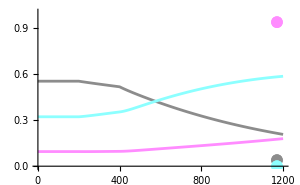
-Graphics-TimeRelative density

```mathematica
fig4a =
Labeled[
Show[
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol4a], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]]],
lb,{Bottom,Left}, RotateLabel->True]
```

#### Abrupt trend same time

```mathematica
MX[t_] := If[t < t0, mx/Sx[yy], pmx mx/Sx[nyy]]/.PARAM4a ; 
MY[t_] := If[t < t0,my/Sy[yy], my/Sy[nyy]]/.PARAM4a ; 
MZ[t_] := If[t < t0,mz/Sz[yy], mz/ Sz[nyy]]/.PARAM4a ; 

F[t_]:= f /.PARAM4a  ;
G[t_] :=g /.PARAM4a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol4b= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

#### Abrupt trend early deforestation

```mathematica
MX[t_] := Which[t < t0, mx/Sx[yy], t0≤ t < t0 + dp,pmx mx/Sx[yy], t≥  t0 +dp , pmx mx/Sx[nyy]]/.PARAM4a ; 
MY[t_] := If[t < t0 +dp ,my/Sy[yy], my/Sy[nyy]]/.PARAM4a ; 
MZ[t_] := If[t < t0  +dp ,mz/Sz[yy], mz/ Sz[nyy]]/.PARAM4a ; 

F[t_]:= f /.PARAM4a  ;
G[t_] :=g /.PARAM4a ;

time = t0 +dt;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

sol4c= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM4a,{x,y,z},{t,0,time},AccuracyGoal->10];
```

### Compile panels

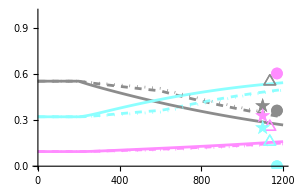
-Graphics-TimeRelative density

```mathematica
fig4a =
Labeled[
Show[
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol4a], {t,0,time},PlotStyle->col2, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol4b], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
Plot[Evaluate[{x[t],y[t],z[t](*, x[t] +y[t]+z[t]*)}/.sol4c], {t,0,time},PlotStyle->col3, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{Automatic,Automatic}, AxesOrigin->{0,0}],
ListPlot[XYF, PlotStyle->col, PlotMarkers->Style["●", 12]],
ListPlot[XYFD, PlotStyle->col, PlotMarkers->Style["△", 14]],
ListPlot[XYFC, PlotStyle->col, PlotMarkers->Style["★", 16]]],
lb,{Bottom,Left}, RotateLabel->True]
```

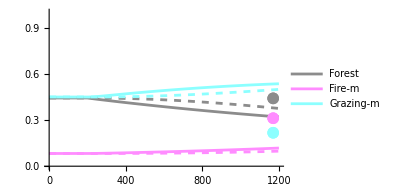
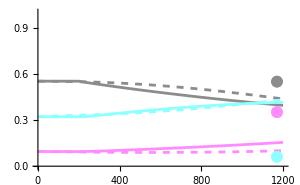
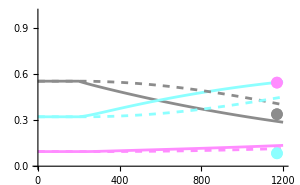
-Graphics-TimeRelative density | -Graphics-TimeRelative density | -Graphics-TimeRelative density

```mathematica
fig3 = Legended[Grid[{{fig3a,fig3b,fig3c}}, Spacings->0.5],lg]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig3_transient.png",fig3, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig3_transient.png

## Figure 5: real climate

Hempson et al., 2015
Highest probability of GM establishment : 400 - 850 mm precip
FM : 850 - 1500 mm

minimum dry season precipitation necessary for forest establishment 50 mm

{1175 + (1175- 625),1175,625}

### vc = 300

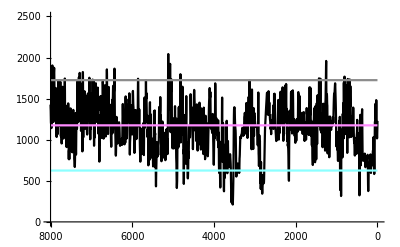

```mathematica
vC = 300;
temp = Import["/Users/tanjona/Box Sync/projects/Grassland_Holocene/data/Li2020_speleo_Rodrigues.csv"][[3;;]];
temp1 = Interpolation[temp];
hum[t_] :=  yy -vC temp1[8000-t];
fig5t =Plot[{hum[8000-x],xx, yy,zz},{x,0,8000}, ScalingFunctions-> {"Reverse", Automatic}, AxesOrigin->{8000,0}, PlotStyle->{Black,colx,coly,colz}, LabelStyle->ls, PlotRange->{All, {0,2500}}]
```

```mathematica
(* Creating initial condition corresponding to the first 500 years *)
iClim = Table[hum[i],{i,1,500,5}]//Mean
PARAM5a = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;

MX[t_] := mx/ Sx[iClim]/.PARAM5a  ; 
MY[t_] := my/ Sy[iClim]/.PARAM5a ;
MZ[t_] :=mz /Sz[iClim]/.PARAM5a  ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten
```

1313.58

{0.622923,0.0619506,0.27998}

#### Default no deforestation mean C = yy, vc = 300

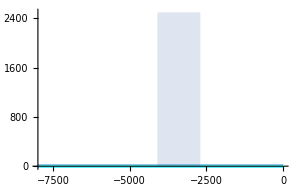
-Graphics-Time BP (yr) Proprotion

```mathematica
(* Running actual simulation *)
MX[t_] := mx/ Sx[hum[t]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5a =
Labeled[Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
],
lb,{Bottom,Left}, RotateLabel->True]
```

```mathematica
fig5aa =
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,0.9}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, Ticks->{None, Automatic}],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
]
```

-Graphics-

#### Default with double deforestation at 4000 BP (4000 in the parametrization), mean C = yy, vc = 200

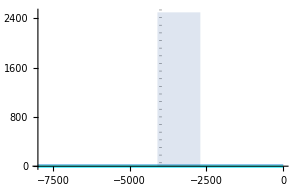
-Graphics-Time BP (yr) Proprotion

```mathematica
tmx = 4000;
MX[t_] :=If[t < tmx, mx/ Sx[hum[t]], mx + mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5b =
Labeled[
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
],
lb,{Bottom,Left}, RotateLabel->True]
```

```mathematica
fig5bb =
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,0.9}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, Ticks->{None, Automatic}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
]
```

-Graphics-

#### Default with double deforestation at 3000 BP (5000 in the parametrization), mean C = yy, vc = 200

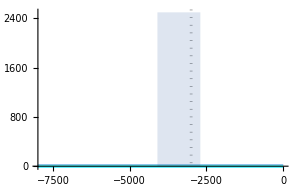
-Graphics-Time BP (yr) Proprotion

```mathematica
tmx = 5000;
MX[t_] :=If[t < 5000, mx/ Sx[hum[t]],mx+mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5c =
Labeled[
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
],
lb,{Bottom,Left}, RotateLabel->True]
```

```mathematica
fig5cc =
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,0.9}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, Ticks->{None, Automatic}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]
]
```

-Graphics-

#### Default with double deforestation at 2000 BP (6000 in the parametrization), mean C = yy

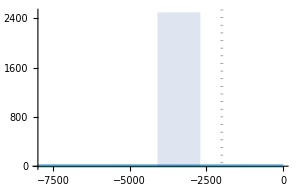
-Graphics-Time BP (yr) Proprotion

```mathematica
tmx = 6000;
MX[t_] :=If[t <tmx, mx/ Sx[hum[t]],mx + mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5d =
Labeled[
Show[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]],
lb,{Bottom,Left}, RotateLabel->True]
```

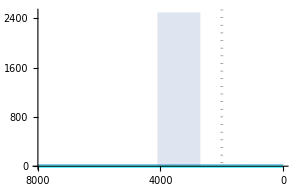

```mathematica
fig5dd =
Show[Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{-0.025,0.9}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,-0.025}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
Plot[2500, {x, 2700,4100},ScalingFunctions-> {"Reverse", Automatic},Filling->Bottom, PlotStyle->None]]
```

### vC = 350

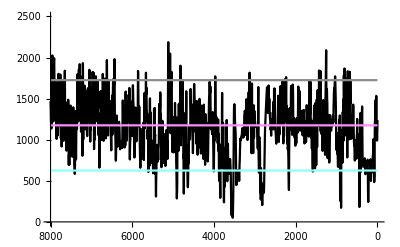

```mathematica
vC = 350;
temp = Import["/Users/tanjona/Box Sync/projects/Grassland_Holocene/data/Li2020_speleo_Rodrigues.csv"][[3;;]];
temp1 = Interpolation[temp];
hum[t_] :=  yy -vC temp1[8000-t];
fig5t =Plot[{hum[8000-x],xx, yy,zz},{x,0,8000}, ScalingFunctions-> {"Reverse", Automatic}, AxesOrigin->{8000,0}, PlotStyle->{Black,colx,coly,colz}, LabelStyle->ls, PlotRange->{All, {0,2500}}]
```

```mathematica
(* Creating initial condition corresponding to the first 500 years *)
iClim = Table[hum[i],{i,1,500,5}]//Mean
PARAM5a = {cx -> 0.01, cy -> 0.05, cz -> 0.05, mx ->0.0005, my -> 0.001, mz -> 0.001, f -> 0.825,g -> 0.975}//Association;

MX[t_] := mx/ Sx[iClim]/.PARAM5a  ; 
MY[t_] := my/ Sy[iClim]/.PARAM5a ;
MZ[t_] :=mz /Sz[iClim]/.PARAM5a  ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

INIT = {0.5,0.3,0.2};
timeEQ = 100000;
solEQ= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,timeEQ},AccuracyGoal->10];
INIT = {x[timeEQ], y[timeEQ], z[timeEQ]} /.solEQ//Flatten
```

1336.67

{0.636401,0.0566678,0.27096}

#### no deforestation mean C = yy

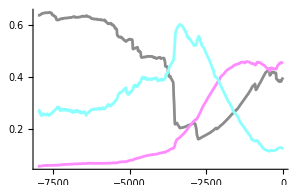
-Graphics-TimeRelative density

```mathematica
(* Running actual simulation *)
MX[t_] := mx/ Sx[hum[t]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5e =
Labeled[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}],
lb,{Bottom,Left}, RotateLabel->True]
```

#### Default with double deforestation at 4000 BP (4000 in the parametrization), mean C = yy, vc = 200

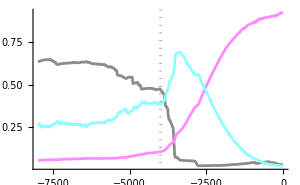
-Graphics-TimeRelative density

```mathematica
tmx = 4000;
MX[t_] :=If[t < tmx, mx/ Sx[hum[t]],2 mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5f =
Labeled[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
lb,{Bottom,Left}, RotateLabel->True]
```

#### Default with double deforestation at 3000 BP (5000 in the parametrization), mean C = yy

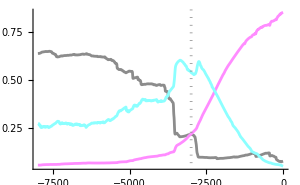
-Graphics-TimeRelative density

```mathematica
tmx = 5000;
MX[t_] :=If[t < tmx, mx/ Sx[hum[t]],2 mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5g =
Labeled[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
lb,{Bottom,Left}, RotateLabel->True]
```

#### Default with double deforestation at 2000 BP (6000 in the parametrization), mean C = yy

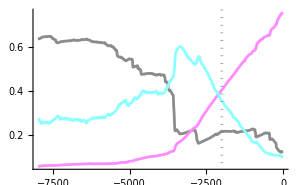
-Graphics-TimeRelative density

```mathematica
tmx = 6000; 
MX[t_] :=If[t < tmx, mx/ Sx[hum[t]],2 mx/ Sx[hum[t]]]/.PARAM5a  ; 
MY[t_] := my/ Sy[hum[t]]/.PARAM5a  ;
MZ[t_] :=mz /Sz[hum[t]]/.PARAM5a ;

F[t_]:= f/.PARAM5a  ;
G[t_] :=g /.PARAM5a ;

FMAT = {
 x[t] (cx (1 - x[t] -  F[t] y[t] - G[t] z[t])- MX[t]) ,
y[t] (cy (1 - x[t]- y[t] -  G[t] z[t])- MY[t]  - (1- F[t]) cx x[t]) , 
z[t] (cz (1 - x[t]- y[t] -z[t]) - MZ[t] - (1-G[t])(cx x[t] + cy y[t]))
};

time = 8000;
sol= NDSolve[{x'[t] == FMAT[[1]], y'[t] == FMAT[[2]], z'[t] == FMAT[[3]],x[0]==INIT[[1]],y[0]==INIT[[2]],z[0]==INIT[[3]]}/.PARAM5a,{x,y,z},{t,0,time},AccuracyGoal->10];

fig5h =
Labeled[
Plot[Evaluate[{x[time- t],y[time - t],z[time -t]}/.sol], {t,0,time},PlotStyle->col, PlotRange->{{0,time},{0,1}}, LabelStyle->{Black,14, FontFamily->"Arial"},ImageSize->is, ScalingFunctions->{"Reverse",Automatic}, AxesOrigin->{time,0}, GridLines->{{time- tmx},None}, GridLinesStyle->Directive[Dotted,Gray, AbsoluteThickness[2]]],
lb,{Bottom,Left}, RotateLabel->True]
```

### Compile figure

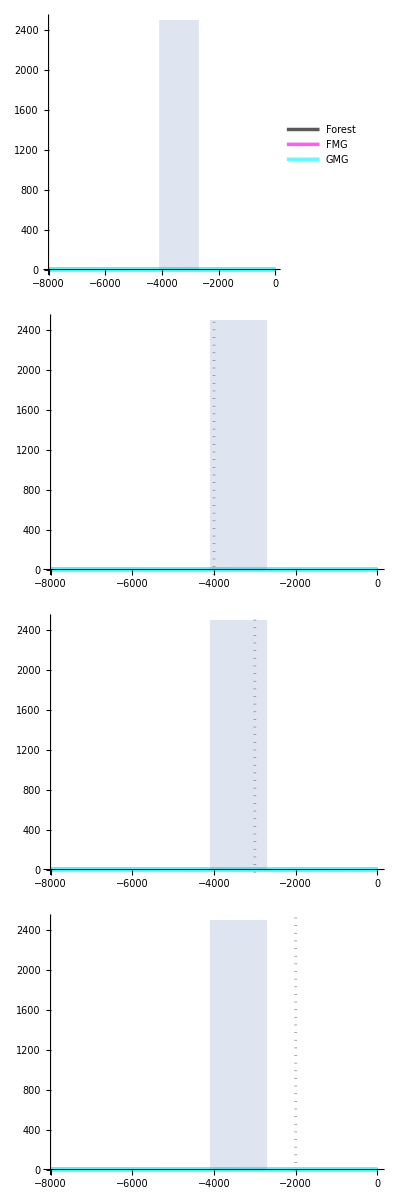
-Graphics-Time BP (yr) Proprotion

```mathematica
fig5 =Legended[
Labeled[
 Grid[{{fig5aa,fig5bb,fig5cc,fig5dd}}//Transpose,Spacings->{0,0}],lb,{Bottom,Left}, RotateLabel->True],lg]
```

```mathematica
Export["/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig5_ts.png",fig5, ImageResolution->150]
```

/Users/tanjona/Box Sync/projects/Grassland_Holocene/figs/fig5_ts.png